This MATHEMATICA script plots the wall solution!

```mathematica
Quit[]
```

```mathematica
l1 = 1;
l2 = 10;
T = 2;
```

```mathematica
λmax = 1/l1+1/l2;
λmin = 1/l1-1/l2;
λ0 = Sqrt[λmax λmin];
A = (λmax^2-λ^2)  (λ^2-λmin^2);
M = (2 Pi T)^2;
```

```mathematica
λ=λmin+ 1/(100l2);
A=(λmax^2-λ^2) (λ^2-λmin^2);
B=2 λ^2 M;
```

```mathematica
s1 = 0;
s2 = -2 B/A;
h1 = l1 Sqrt[M];
h2 = l2 Sqrt[M];
```

```mathematica
α1= -(λ^2+λ0^2)/Sqrt[A (s2+h1^2)];
α2= -(λ^2-λ0^2)/Sqrt[A (s2+h2^2)];
β1=1/Sqrt[h1^2+s2];
β2=1/Sqrt[h2^2+s2];
```

```mathematica
x1[σ_]=α1 ArcTan[β1 Sqrt[σ-s2]];
x2[σ_]=α2 ArcTan[β2 Sqrt[σ-s2]];
```

```mathematica
tonum = (#//. {l1-> 1, l2-> 10 })&;
```

```mathematica
Plot[{x1[σ]},{σ,0,100}]
```

```mathematica
σgrid = Array[#&,100000,{0,100000000}];
```

```mathematica
f1 = Table[x1[i], {i, σgrid}]//Re//N;
f2 = Table[x2[i], {i, σgrid}]//Re//N;
```

```mathematica
p1=ListPlot[Transpose[{σgrid, f1}]];
p2=ListPlot[Transpose[{σgrid, f2}]];
```

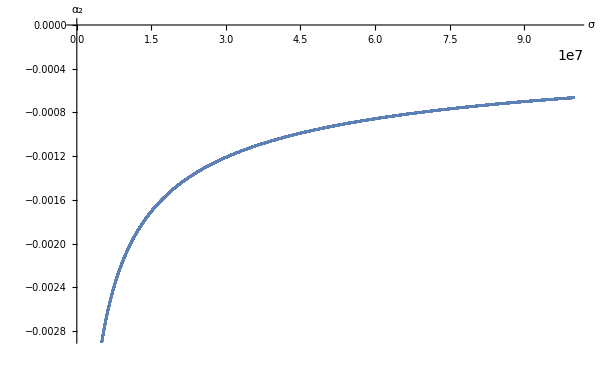

```mathematica
Show[p2,AxesLabel->{HoldForm[σ],HoldForm[Subscript[α, 2]]},PlotLabel->None,LabelStyle->{FontFamily->"Al Bayan",10,GrayLevel[0]}]
```

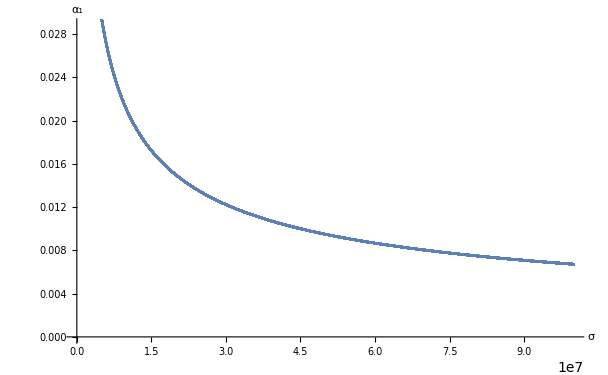

```mathematica
Show[p1,AxesLabel->{HoldForm[σ],HoldForm[Subscript[α, 1]]},PlotLabel->None,LabelStyle->{FontFamily->"Al Bayan",10,GrayLevel[0]}]
```